```mathematica
(*This first part is what you already know*)
```

```mathematica
Clear[kt,u, d,g,rs, a, b,x, rho1,rho2,rho3, rhodash, rhodash1, rhodash2,rhodash3, lgs, lgs1,lgs2, lgs3,lgs4,lgs5,lgs6,k,fk,kulim0,kliminf,dk]
```

```mathematica
kt = 1;
rs = 1;
```

```mathematica
(*Transition matrix for Barrier*)
```

```mathematica
w = {{-g,g},{g,-g}};
```

```mathematica
(*evec = Eigenvectors[w] Use hard coded definition instead to assure correct order of eigenvalues *)
```

```mathematica
evec = {{1,1},{-1,1}}
```

{{1,1},{-1,1}}

```mathematica
s = Transpose[{Normalize[evec[[1]]],Normalize[evec[[2]]]}]
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
invs = Simplify[Assuming[{ab>0, ba>0},Inverse[s]]]
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
diagw = Simplify[invs.w.s]
```

{{0,0},{0,-2 g}}

```mathematica
(*Assembly of matching matrix*)
```

```mathematica
bcu = {{1,0},{0,Exp[u/kt]}}
```

{{1,0},{0,ⅇ^u}}

```mathematica
(*Do handy substitutions first before things get out of hand!*)
```

```mathematica
rhodash[r_] = {{1, 1/r, 0, 0},{0, 0, Exp[-Sqrt[Abs[diagw[[2,2]]]/d]r]/r,Exp[Sqrt[Abs[diagw[[2,2]]]/d]r]/r}} /.√2 √(1/d) √Abs[g]->x
```

{{1,1/r,0,0},{0,0,ⅇ^(-r x)/r,ⅇ^(r x)/r}}

```mathematica
(*Build system of linear equations for fitting and boundary conditions*)
```

```mathematica
lgs1 = Join[rhodash[rs],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];
lgs2 = Join[rhodash[a], -invs.bcu.s.rhodash[a], {{0,0,0,0},{0,0,0,0}},2];
lgs3 = Join[rhodash'[a],-rhodash'[a],{{0,0,0,0},{0,0,0,0}},2];
lgs4= Join[{{0,0,0,0},{0,0,0,0}},invs.bcu.s.rhodash[b],-rhodash[b],2];
lgs5 = Join[{{0,0,0,0},{0,0,0,0}},rhodash'[b],-rhodash'[b],2];
lgs6 = Join[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,Infinity}},2];
```

```mathematica
lgs = Join[lgs1, lgs2, lgs3, lgs4,lgs5,lgs6,1];
```

```mathematica
lgs = lgs[[1;;11,1;;11]];
```

```mathematica
(*Calculation of matching constants*)
```

```mathematica
c =Assuming[{g>0,d>0,kt>0,b>a>rs>0}, LinearSolve[lgs,Transpose[{{0,0,0,0,0,0,0,0,0,0,1}}]]];
```

```mathematica
c = Assuming[b > a > rs > 0,Simplify[c]];
```

```mathematica
c = Join[c,{{0}}];
```

```mathematica
(*Check, if matching worked out*)
```

```mathematica
Simplify[lgs.c[[1;;11]]]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}}

```mathematica
rhodash1[r_] = rhodash[r].c[[1;;4]];
```

```mathematica
Simplify[rhodash1[rs]]
```

{{0},{0}}

```mathematica
rhodash2[r_] = rhodash[r].c[[5;;8]];
```

```mathematica
rhodash3[r_] = rhodash[r].c[[9;;12]];
```

```mathematica
Simplify[invs.bcu.s.rhodash2[b] - rhodash3[b]]
Simplify[rhodash2'[b] - rhodash3'[b]]
Simplify[rhodash3[Infinity]]
```

{{0},{0}}

{{0},{0}}

{{1},{0 ⅇ^(x (-∞))}}

```mathematica
(*Calculatio normalization of density profiles*)
```

```mathematica
n = Limit[Total[Total[s.rhodash3[r]]],r->Infinity]
```

√2

```mathematica
(*Calculate density profiles*)
```

```mathematica
rho1[r_] = s.rhodash1[r]/n;
rho2[r_] = s.rhodash2[r]/n;
rho3[r_] = s.rhodash3[r]/n;
```

```mathematica
rhom1[r_] =Part[rho1[r],1]+ Part[rho1[r],2];
rhom2[r_] =Part[rho2[r],1]+ Part[rho2[r],2];
rhom3[r_] =Part[rho3[r],1]+ Part[rho3[r],2];
```

```mathematica
(*Calculate absorption rate (omit the 4 pi D Rs) such that the result is normalized to the debye result for the ungated problem*)
```

```mathematica
rho1dash[r_] := rhom1'[r]
```

```mathematica
k:=  Simplify[Total[rho1dash[1]]]
```

```mathematica
(*Make absorption rate a function of its parameters*)
```

```mathematica
fk[a_,b_,u_,x_]:=(-2 ⅇ^(u+2 (1+b) x) (1+a x) (-1+b x)-2 b ⅇ^((2+a+b) x) x (1+b x)+2 b ⅇ^((3 a+b) x) x (1+b x)-4 b ⅇ^(u+3 a x+b x) x (1+b x)+2 b ⅇ^(2 u+3 a x+b x) x (1+b x)+4 b ⅇ^(u+(2+a+b) x) x (1+b x)-2 b ⅇ^(2 u+(2+a+b) x) x (1+b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-ⅇ^(2 (1+a) x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (-1+a x) (1+b x)-2 ⅇ^(u+2 (1+a) x) (1+a x) (1+b x)-ⅇ^(2 (u+x+b x)) (1+a x) (1+b x)-ⅇ^(2 (u+(a+b) x)) (-1+3 a x) (1+b x)+ⅇ^(2 (u+x+a x)) (1+3 a x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+3 b x)-ⅇ^(2 (a+b) x) (1+a x) (-1+3 b x)+2 ⅇ^(u+2 (a+b) x) (-1+b x+a (x-5 b x^2)))/(2 ⅇ^(u+2 (1+b) x) (1+a x) (1+(-2+b) x)+2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)-4 ⅇ^(u+(2+a+b) x) x (-2+a-a x+a^2 x-b x)+2 ⅇ^(2 u+(2+a+b) x) x (-2+a-a x+a^2 x-b x)+2 ⅇ^(u+2 (1+a) x) (-1+(-2+a) x) (1+b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 (u+x+a x)) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+a) x) (-1+(-2+3 a) x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+(2+b) x)-ⅇ^(2 (u+x+b x)) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (u+(a+b) x)) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)-ⅇ^(2 (a+b) x) (-1+(4-3 a+b) x+(-2 b+a (2+3 b)) x^2)-2 ⅇ^(u+2 (a+b) x) (1+(-4+a+b) x+(-2 b+a (2+5 b)) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x))-4 ⅇ^(u+3 a x+b x) x (2+a^2 x+b x-a (1+x))+2 ⅇ^(2 u+3 a x+b x) x (2+a^2 x+b x-a (1+x)))
```

```mathematica
(*Calculate limiting behaviour for x ->0*)
```

```mathematica
Assuming[b > a > 1,Limit[k,x->0]]
```

(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))

```mathematica
klim0[a_,b_,u_]:=(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2(b-b ⅇ^u+a (-1-b+ⅇ^u)))
```

```mathematica
(*Calculate limiting behaviour for x -> oo by hand, since mathematica resists do it... terefore only collect terms with leading exponents from k and simplify the resulting rational function*)
```

```mathematica
Simplify[(-ⅇ^(2 (u+(a+b) x)) (-1+3 a x) (1+b x)-ⅇ^(2 (a+b) x) (1+a x) (-1+3 b x)+2 ⅇ^(u+2 (a+b) x) (-1+b x+a (x-5 b x^2)))/(-ⅇ^(2 (u+(a+b) x)) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)-ⅇ^(2 (a+b) x) (-1+(4-3 a+b) x+(-2 b+a (2+3 b)) x^2)-2 ⅇ^(u+2 (a+b) x) (1+(-4+a+b) x+(-2 b+a (2+5 b)) x^2))]
```

((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2))

```mathematica
(*Then take the limit for x to infinity*)
```

```mathematica
Limit[((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2)),x->Infinity]
```

(a b (3+ⅇ^u))/(2 b (-1+ⅇ^u)+a (2-2 ⅇ^u+b (3+ⅇ^u)))

```mathematica
kliminf[a_,b_,u_]:=(a b (3+ⅇ^u))/(2 b (-1+ⅇ^u)+a (2-2 ⅇ^u+b (3+ⅇ^u)))
```

```mathematica
(*Do some plot of the results*)
```

```mathematica
a = 4;
b = 8;
u = 4;
LogLinearPlot[{fk[a,b,u,x],klim0[a,b,u],kliminf[a,b,u]}, {x,0.001,1000},PlotRange->{{0.01,100},{1,1.4}},AxesLabel->{alpha, K/Kd}]
Clear[a,b,u,x]
```

-Graphics-

```mathematica
(*Limiting behaviour is somewhat different from what we expected and not very intuitive to understand at first glance... BUT this looks a lot better than everything i've had so far.*)
```

```mathematica
(*Now lets have a look at the approximate behaviour of k for x->oo and x->0.*)
```

```mathematica
(*Therefore for x->oo collect the terms with largest exponent from numerator and denominator of k*)
```

```mathematica
klargex =Simplify[((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2))]
```

((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2))

```mathematica
Collect[((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x))),x]
```

-1+2 ⅇ^u-ⅇ^(2 u)+(-a+3 b-2 a ⅇ^u-2 b ⅇ^u+3 a ⅇ^(2 u)-b ⅇ^(2 u)) x+(3 a b+10 a b ⅇ^u+3 a b ⅇ^(2 u)) x^2

```mathematica
Collect[(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2)),x]
```

-1+2 ⅇ^u-ⅇ^(2 u)+(4-3 a+b+2 (-4+a+b) ⅇ^u+(4+a-3 b) ⅇ^(2 u)) x+(2 a-2 b+3 a b+2 (2 a-2 b+5 a b) ⅇ^u+3 (a (-2+b)+2 b) ⅇ^(2 u)) x^2

```mathematica
(*Then, from each collect the leading terms in x and simplify*)
```

```mathematica
fklargex[a_,b_,u_,x_] := Simplify[(-1+2 ⅇ^u-ⅇ^(2 u)+(-a+3 b-2 a ⅇ^u-2 b ⅇ^u+3 a ⅇ^(2 u)-b ⅇ^(2 u)) x+(3 a b+10 a b ⅇ^u+3 a b ⅇ^(2 u)) x^2)/(-1+2 ⅇ^u-ⅇ^(2 u)+(4-3 a+b+2 (-4+a+b) ⅇ^u+(4+a-3 b) ⅇ^(2 u)) x+(2 a-2 b+3 a b+2 (2 a-2 b+5 a b) ⅇ^u+3 (a (-2+b)+2 b) ⅇ^(2 u)) x^2)]
```

```mathematica
(*For x->0 do taylor expansion*)
```

```mathematica
ksmallx =Simplify[Series[k,{x,0,2}]]
```

(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))+((a-b)^2 (-1+ⅇ^u)^2 x)/(4 (a (1+b-ⅇ^u)+b (-1+ⅇ^u))^2)+((a-b)^2 ⅇ^-u (-1+ⅇ^u)^2 (-2 a^4 b (1+b-ⅇ^u)-a^3 b (-5+b^2+6 ⅇ^u-ⅇ^(2 u)+2 b (-3+ⅇ^u))+b (-1+ⅇ^u) (-ⅇ^u+3 b^2 (-1+ⅇ^u))-a^2 b (-4 b (-1+ⅇ^u)+3 (-1+ⅇ^u)^2+b^2 (-5+2 ⅇ^u))-a (4 b ⅇ^u-ⅇ^u (-1+ⅇ^u)+b^3 (7-8 ⅇ^u+ⅇ^(2 u)))) x^2)/(24 (b-b ⅇ^u+a (-1-b+ⅇ^u))^3)+O[x]^3

```mathematica
fksmallx[a_,b_,u_,x_] :=(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))+((a-b)^2 (-1+ⅇ^u)^2 x)/(4 (a (1+b-ⅇ^u)+b (-1+ⅇ^u))^2)+1/(24 (b-b ⅇ^u+a (-1-b+ⅇ^u))^3)(a-b)^2 ⅇ^-u (-1+ⅇ^u)^2 (-2 a^4 b (1+b-ⅇ^u)-a^3 b (-5+b^2+6 ⅇ^u-ⅇ^(2 u)+2 b (-3+ⅇ^u))+b (-1+ⅇ^u) (-ⅇ^u+3 b^2 (-1+ⅇ^u))-a^2 b (-4 b (-1+ⅇ^u)+3 (-1+ⅇ^u)^2+b^2 (-5+2 ⅇ^u))-a (4 b ⅇ^u-ⅇ^u (-1+ⅇ^u)+b^3 (7-8 ⅇ^u+ⅇ^(2 u)))) x^2
```

```mathematica
(* See some examplary plots for the results*)
```

```mathematica
Needs["PlotLegends`"]
```

4

6

4

0.3

0.2

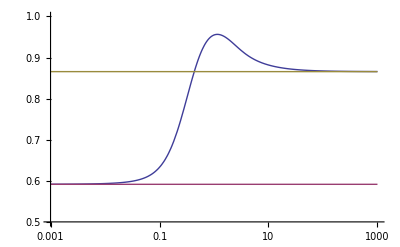

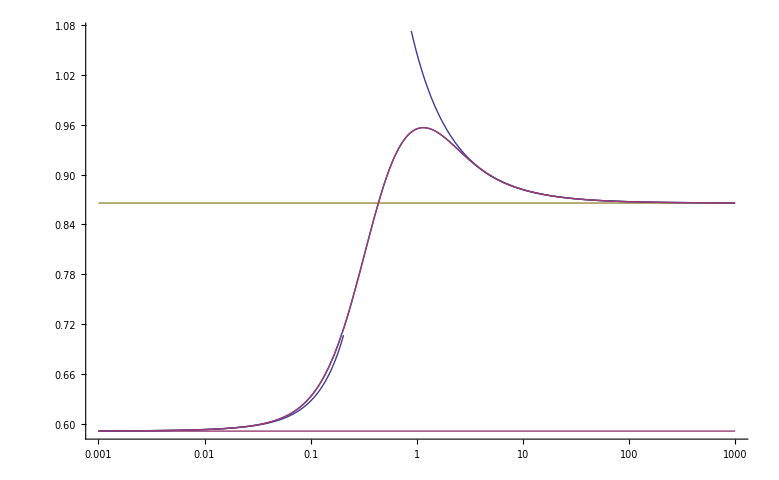

```mathematica
a = 4
b = 6
u = 4
pmax =0.3
pmin =0.2
p1 =LogLinearPlot[{fk[a,b,u,x],klim0[a,b,u],kliminf[a,b,u]}, {x,0.001,1000},PlotRange->{{-7,7},{0.5,1}}];
p2 =LogLinearPlot[{fklargex[a,b,u,x],fk[a,b,u,x]}, {x,pmin,1000}];
p3 =LogLinearPlot[{fksmallx[a,b,u,x],fk[a,b,u,x]}, {x,0.001,pmax}];
Show[p1]
Show[p1,p2,p3,PlotRange -> All]
Clear[a,b,u,x]
```

```mathematica
(*Calculate limiting cases for |u|->Infinity*)
```

```mathematica
klimuplus = Simplify[Limit[Collect[Numerator[k],ⅇ^u]/Collect[Denominator[k],ⅇ^u],u->Infinity]]
```

((1+b x) (-2 b ⅇ^((2+a+b) x) x+2 b ⅇ^((3 a+b) x) x+ⅇ^(2 (a+b) x) (1-3 a x)+ⅇ^(4 a x) (-1+a x)-ⅇ^(2 (1+b) x) (1+a x)+ⅇ^(2 (1+a) x) (1+3 a x)))/(2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)+ⅇ^(4 a x) (-1+a x) (1+b x)+ⅇ^(2 (1+a) x) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+b) x) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (a+b) x) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x)))

```mathematica
fklimuplus[a_,b_,x_]:=-((1+b x) (2 b ⅇ^((2+a+b) x) x-2 b ⅇ^((3 a+b) x) x+ⅇ^(4 a x) (1-a x)+ⅇ^(2 (1+b) x) (1+a x)+ⅇ^(2 (a+b) x) (-1+3 a x)-ⅇ^(2 (1+a) x) (1+3 a x)))/(2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)+ⅇ^(4 a x) (-1+a x) (1+b x)+ⅇ^(2 (1+a) x) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+b) x) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (a+b) x) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x)))
```

```mathematica
Collect[ⅇ^(-2u)*Numerator[k],ⅇ^-u]
```

-ⅇ^(4 a x)+ⅇ^(2 (a+b) x)+ⅇ^(2 x+2 a x)-ⅇ^(2 x+2 b x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x-3 a ⅇ^(2 (a+b) x) x+b ⅇ^(2 (a+b) x) x-2 b ⅇ^((2+a+b) x) x+3 a ⅇ^(2 x+2 a x) x+b ⅇ^(2 x+2 a x) x+2 b ⅇ^(3 a x+b x) x-a ⅇ^(2 x+2 b x) x-b ⅇ^(2 x+2 b x) x+a b ⅇ^(4 a x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 b^2 ⅇ^((2+a+b) x) x^2+3 a b ⅇ^(2 x+2 a x) x^2+2 b^2 ⅇ^(3 a x+b x) x^2-a b ⅇ^(2 x+2 b x) x^2+ⅇ^(-2 u) (-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x-a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x-a ⅇ^(2 (1+b) x) x+3 b ⅇ^(2 (1+b) x) x+a ⅇ^(2 (a+b) x) x-3 b ⅇ^(2 (a+b) x) x-2 b ⅇ^((2+a+b) x) x+2 b ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2-a b ⅇ^(2 (1+a) x) x^2+3 a b ⅇ^(2 (1+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 b^2 ⅇ^((2+a+b) x) x^2+2 b^2 ⅇ^((3 a+b) x) x^2)+ⅇ^-u (2 ⅇ^(4 a x)-2 ⅇ^(2 (1+a) x)+2 ⅇ^(2 (1+b) x)-2 ⅇ^(2 (a+b) x)-2 a ⅇ^(4 a x) x+2 b ⅇ^(4 a x) x-2 a ⅇ^(2 (1+a) x) x-2 b ⅇ^(2 (1+a) x) x+2 a ⅇ^(2 (1+b) x) x-2 b ⅇ^(2 (1+b) x) x+2 a ⅇ^(2 (a+b) x) x+2 b ⅇ^(2 (a+b) x) x+4 b ⅇ^((2+a+b) x) x-4 b ⅇ^(3 a x+b x) x-2 a b ⅇ^(4 a x) x^2-2 a b ⅇ^(2 (1+a) x) x^2-2 a b ⅇ^(2 (1+b) x) x^2-10 a b ⅇ^(2 (a+b) x) x^2+4 b^2 ⅇ^((2+a+b) x) x^2-4 b^2 ⅇ^(3 a x+b x) x^2)

```mathematica
Collect[ⅇ^(-2u)*Denominator[k],ⅇ^-u]
```

-ⅇ^(4 a x)+ⅇ^(2 (a+b) x)+ⅇ^(2 x+2 a x)-ⅇ^(2 x+2 b x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x-4 ⅇ^(2 (a+b) x) x-a ⅇ^(2 (a+b) x) x+3 b ⅇ^(2 (a+b) x) x-4 ⅇ^((2+a+b) x) x+2 a ⅇ^((2+a+b) x) x+2 ⅇ^(2 x+2 a x) x+a ⅇ^(2 x+2 a x) x+b ⅇ^(2 x+2 a x) x+4 ⅇ^(3 a x+b x) x-2 a ⅇ^(3 a x+b x) x+2 ⅇ^(2 x+2 b x) x-a ⅇ^(2 x+2 b x) x-3 b ⅇ^(2 x+2 b x) x+a b ⅇ^(4 a x) x^2+6 a ⅇ^(2 (a+b) x) x^2-6 b ⅇ^(2 (a+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 a ⅇ^((2+a+b) x) x^2+2 a^2 ⅇ^((2+a+b) x) x^2-2 b ⅇ^((2+a+b) x) x^2+2 b ⅇ^(2 x+2 a x) x^2+a b ⅇ^(2 x+2 a x) x^2-2 a ⅇ^(3 a x+b x) x^2+2 a^2 ⅇ^(3 a x+b x) x^2+2 b ⅇ^(3 a x+b x) x^2+2 a ⅇ^(2 x+2 b x) x^2-3 a b ⅇ^(2 x+2 b x) x^2+ⅇ^(-2 u) (-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x+2 ⅇ^(2 (1+a) x) x-3 a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x+2 ⅇ^(2 (1+b) x) x-a ⅇ^(2 (1+b) x) x+b ⅇ^(2 (1+b) x) x-4 ⅇ^(2 (a+b) x) x+3 a ⅇ^(2 (a+b) x) x-b ⅇ^(2 (a+b) x) x-4 ⅇ^((2+a+b) x) x+2 a ⅇ^((2+a+b) x) x+4 ⅇ^((3 a+b) x) x-2 a ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2+2 b ⅇ^(2 (1+a) x) x^2-3 a b ⅇ^(2 (1+a) x) x^2+2 a ⅇ^(2 (1+b) x) x^2+a b ⅇ^(2 (1+b) x) x^2-2 a ⅇ^(2 (a+b) x) x^2+2 b ⅇ^(2 (a+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 a ⅇ^((2+a+b) x) x^2+2 a^2 ⅇ^((2+a+b) x) x^2-2 b ⅇ^((2+a+b) x) x^2-2 a ⅇ^((3 a+b) x) x^2+2 a^2 ⅇ^((3 a+b) x) x^2+2 b ⅇ^((3 a+b) x) x^2)+ⅇ^-u (2 ⅇ^(4 a x)-2 ⅇ^(2 (1+a) x)+2 ⅇ^(2 (1+b) x)-2 ⅇ^(2 (a+b) x)-2 a ⅇ^(4 a x) x+2 b ⅇ^(4 a x) x-4 ⅇ^(2 (1+a) x) x+2 a ⅇ^(2 (1+a) x) x-2 b ⅇ^(2 (1+a) x) x-4 ⅇ^(2 (1+b) x) x+2 a ⅇ^(2 (1+b) x) x+2 b ⅇ^(2 (1+b) x) x+8 ⅇ^(2 (a+b) x) x-2 a ⅇ^(2 (a+b) x) x-2 b ⅇ^(2 (a+b) x) x+8 ⅇ^((2+a+b) x) x-4 a ⅇ^((2+a+b) x) x-8 ⅇ^(3 a x+b x) x+4 a ⅇ^(3 a x+b x) x-2 a b ⅇ^(4 a x) x^2-4 b ⅇ^(2 (1+a) x) x^2+2 a b ⅇ^(2 (1+a) x) x^2-4 a ⅇ^(2 (1+b) x) x^2+2 a b ⅇ^(2 (1+b) x) x^2-4 a ⅇ^(2 (a+b) x) x^2+4 b ⅇ^(2 (a+b) x) x^2-10 a b ⅇ^(2 (a+b) x) x^2+4 a ⅇ^((2+a+b) x) x^2-4 a^2 ⅇ^((2+a+b) x) x^2+4 b ⅇ^((2+a+b) x) x^2+4 a ⅇ^(3 a x+b x) x^2-4 a^2 ⅇ^(3 a x+b x) x^2-4 b ⅇ^(3 a x+b x) x^2)

```mathematica
Simplify[(-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x-a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x-a ⅇ^(2 (1+b) x) x+3 b ⅇ^(2 (1+b) x) x+a ⅇ^(2 (a+b) x) x-3 b ⅇ^(2 (a+b) x) x-2 b ⅇ^((2+a+b) x) x+2 b ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2-a b ⅇ^(2 (1+a) x) x^2+3 a b ⅇ^(2 (1+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 b^2 ⅇ^((2+a+b) x) x^2+2 b^2 ⅇ^((3 a+b) x) x^2)/(-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x+2 ⅇ^(2 (1+a) x) x-3 a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x+2 ⅇ^(2 (1+b) x) x-a ⅇ^(2 (1+b) x) x+b ⅇ^(2 (1+b) x) x-4 ⅇ^(2 (a+b) x) x+3 a ⅇ^(2 (a+b) x) x-b ⅇ^(2 (a+b) x) x-4 ⅇ^((2+a+b) x) x+2 a ⅇ^((2+a+b) x) x+4 ⅇ^((3 a+b) x) x-2 a ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2+2 b ⅇ^(2 (1+a) x) x^2-3 a b ⅇ^(2 (1+a) x) x^2+2 a ⅇ^(2 (1+b) x) x^2+a b ⅇ^(2 (1+b) x) x^2-2 a ⅇ^(2 (a+b) x) x^2+2 b ⅇ^(2 (a+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 a ⅇ^((2+a+b) x) x^2+2 a^2 ⅇ^((2+a+b) x) x^2-2 b ⅇ^((2+a+b) x) x^2-2 a ⅇ^((3 a+b) x) x^2+2 a^2 ⅇ^((3 a+b) x) x^2+2 b ⅇ^((3 a+b) x) x^2)]
```

(-2 b ⅇ^((2+a+b) x) x (1+b x)+2 b ⅇ^((3 a+b) x) x (1+b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-ⅇ^(2 (1+a) x) (-1+a x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+3 b x)-ⅇ^(2 (a+b) x) (1+a x) (-1+3 b x))/(2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-ⅇ^(2 (1+a) x) (-1+(-2+3 a) x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+(2+b) x)-ⅇ^(2 (a+b) x) (-1+(4-3 a+b) x+(-2 b+a (2+3 b)) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x)))

```mathematica
fklimuminus[a_,b_,x_]:=(-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x-a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x-a ⅇ^(2 (1+b) x) x+3 b ⅇ^(2 (1+b) x) x+a ⅇ^(2 (a+b) x) x-3 b ⅇ^(2 (a+b) x) x-2 b ⅇ^((2+a+b) x) x+2 b ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2-a b ⅇ^(2 (1+a) x) x^2+3 a b ⅇ^(2 (1+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 b^2 ⅇ^((2+a+b) x) x^2+2 b^2 ⅇ^((3 a+b) x) x^2)/(-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x+2 ⅇ^(2 (1+a) x) x-3 a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x+2 ⅇ^(2 (1+b) x) x-a ⅇ^(2 (1+b) x) x+b ⅇ^(2 (1+b) x) x-4 ⅇ^(2 (a+b) x) x+3 a ⅇ^(2 (a+b) x) x-b ⅇ^(2 (a+b) x) x-4 ⅇ^((2+a+b) x) x+2 a ⅇ^((2+a+b) x) x+4 ⅇ^((3 a+b) x) x-2 a ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2+2 b ⅇ^(2 (1+a) x) x^2-3 a b ⅇ^(2 (1+a) x) x^2+2 a ⅇ^(2 (1+b) x) x^2+a b ⅇ^(2 (1+b) x) x^2-2 a ⅇ^(2 (a+b) x) x^2+2 b ⅇ^(2 (a+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 a ⅇ^((2+a+b) x) x^2+2 a^2 ⅇ^((2+a+b) x) x^2-2 b ⅇ^((2+a+b) x) x^2-2 a ⅇ^((3 a+b) x) x^2+2 a^2 ⅇ^((3 a+b) x) x^2+2 b ⅇ^((3 a+b) x) x^2)
```

```mathematica
(*Plot calculated relation. Resonant behaviour still exists*)
```

1.01

1.02

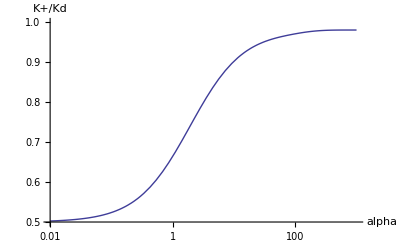

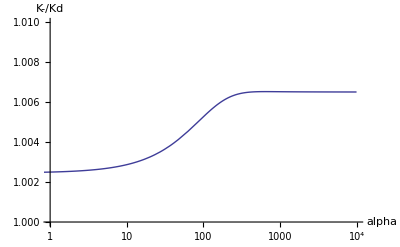

```mathematica
a = 1.01
b = 1.02
p1 =LogLinearPlot[{fklimuplus[a,b,x]}, {x,0.01,1000},AxesLabel->{alpha, "K+/Kd"},PlotRange->{{0.01,1000},{0.5,1}}]
p2 = LogLinearPlot[{fklimuminus[a,b,x]},{x,0.01,10000},AxesLabel->{alpha, "K-/Kd"},PlotRange->{{1,10000},{1.0,1.01}}]
Clear[a,b]
```

```mathematica
(*Intuitive guess: if the diffusion time of particles across the barrier is equal to the inverse of the switching rate, resonance accures. If so, the following plot would be (more or less) constant.. Well, obviously not.*)
a = 2
LogLinearPlot[(x/.Last[FindMaximum[{fklimu[a,b,x]*(a-b),x>0},{x,1}]]),{b,a,a+3}]
```

```mathematica
(*Ok, so if this does not work, lets try to proove, that resonant behaviour does at least allways exist. Therefore do Taylor expansions fo the Limits and show, that their slopes are both positive*)
```

```mathematica
Series[klargex, {x,Infinity, 2}]
```

(a b (3+ⅇ^u))/(2 a-2 b+3 a b-2 a ⅇ^u+2 b ⅇ^u+a b ⅇ^u)+(2 (-1+ⅇ^u)^2 (-a^2-2 a b+3 a^2 b-3 b^2+3 a b^2-3 a^2 ⅇ^u+2 a b ⅇ^u+a^2 b ⅇ^u-b^2 ⅇ^u+a b^2 ⅇ^u))/((1+3 ⅇ^u) (2 a-2 b+3 a b-2 a ⅇ^u+2 b ⅇ^u+a b ⅇ^u)^2 x)+1/x^2(((1-ⅇ^u) (-1+ⅇ^u))/((1+3 ⅇ^u) (2 a-2 b+3 a b-2 a ⅇ^u+2 b ⅇ^u+a b ⅇ^u))-((4-3 a+b+2 (-4+a+b) ⅇ^u+(4+a-3 b) ⅇ^(2 u)) (b (1-ⅇ^u) (3+ⅇ^u)+(-1+ⅇ^u) (a+3 a ⅇ^u)))/((1+3 ⅇ^u)^2 (2 a-2 b+3 a b-2 a ⅇ^u+2 b ⅇ^u+a b ⅇ^u)^2)+(b (3+ⅇ^u) (a+3 a ⅇ^u) (((-1+ⅇ^u)^2)/((1+3 ⅇ^u) (2 a-2 b+3 a b-2 a ⅇ^u+2 b ⅇ^u+a b ⅇ^u))+((4-3 a+b+2 (-4+a+b) ⅇ^u+(4+a-3 b) ⅇ^(2 u))^2)/((1+3 ⅇ^u)^2 (2 a-2 b+3 a b-2 a ⅇ^u+2 b ⅇ^u+a b ⅇ^u)^2)))/((1+3 ⅇ^u) (2 a-2 b+3 a b-2 a ⅇ^u+2 b ⅇ^u+a b ⅇ^u)))+O[1/x]^3

```mathematica
klxnumerator[a_,t_,u_] := (-a^2-2 a b+3 a^2 b-3 b^2+3 a b^2-3 a^2 ⅇ^u+2 a b ⅇ^u+a^2 b ⅇ^u-b^2 ⅇ^u+a b^2 ⅇ^u)/.b ->a+t
```

```mathematica
Assuming[{b>a>0,u>0},Simplify[ (-a^2-2 a b+3 a^2 b-3 b^2+3 a b^2-3 a^2 ⅇ^u+2 a b ⅇ^u+a^2 b ⅇ^u-b^2 ⅇ^u+a b^2 ⅇ^u)>0]]
```

```mathematica
Simplify[b(b (-1-3 ⅇ^u+b (3+ⅇ^u))+b (2 (-1+ⅇ^u)+b (3+ⅇ^u)))>b^2 (3+ⅇ^u)]
```

(-1+b) b^2 (3+ⅇ^u)>0

```mathematica
(*Well, the following plot shows, that in the relevant parameter range, this is true. Sadly I have not been able to show this in generall so far.*)
```

```mathematica
RegionPlot3D[(-a^2-2 a b+3 a^2 b-3 b^2+3 a b^2-3 a^2 ⅇ^u+2 a b ⅇ^u+a^2 b ⅇ^u-b^2 ⅇ^u+a b^2 ⅇ^u)<=0&&a<b,{b,1,2},{u,-5,5},{a,1,2},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*Next guess. The limit of a locally one dimensional problem i.e. a/(b-a) = constant, a->0 might be interesting*)
```

```mathematica
(*First do necessary substitutions*)
```

```mathematica
Simplify[-((1+b x) (2 b ⅇ^((2+a+b) x) x-2 b ⅇ^((3 a+b) x) x+ⅇ^(4 a x) (1-a x)+ⅇ^(2 (1+b) x) (1+a x)+ⅇ^(2 (a+b) x) (-1+3 a x)-ⅇ^(2 (1+a) x) (1+3 a x)))/(2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)+ⅇ^(4 a x) (-1+a x) (1+b x)+ⅇ^(2 (1+a) x) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+b) x) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (a+b) x) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x)))/.b->1+(1+g)*t]
```

```mathematica
Simplify[-((1+(1+t+g t) x) (2 ⅇ^((3+a+t+g t) x) (1+t+g t) x-2 ⅇ^((1+3 a+t+g t) x) (1+t+g t) x+ⅇ^(4 a x) (1-a x)+ⅇ^(2 (2+t+g t) x) (1+a x)+ⅇ^(2 (1+a+t+g t) x) (-1+3 a x)-ⅇ^(2 (1+a) x) (1+3 a x)))/(2 ⅇ^((3+a+t+g t) x) x (-2+a-a x+a^2 x-(1+t+g t) x)+ⅇ^(4 a x) (-1+a x) (1+(1+t+g t) x)+ⅇ^(2 (1+a) x) (1+(2+a) x) (1+(1+t+g t) x)-ⅇ^(2 (2+t+g t) x) (1+a x) (1+(1+3 (1+g) t) x)-ⅇ^(2 (1+a+t+g t) x) (-1+(1+a-3 (1+g) t) x+3 (a (-1+t+g t)+2 (1+t+g t)) x^2)+2 ⅇ^((1+3 a+t+g t) x) x (2+a^2 x+(1+t+g t) x-a (1+x)))/.a->1+t]
```

-((1+(1+t+g t) x) (2 ⅇ^((4+(2+g) t) x) (1+t+g t) x-2 ⅇ^((4+(4+g) t) x) (1+t+g t) x-ⅇ^(4 (1+t) x) (-1+x+t x)+ⅇ^(2 (2+t+g t) x) (1+x+t x)+ⅇ^(2 (2+(2+g) t) x) (-1+3 (1+t) x)-ⅇ^(2 (2+t) x) (1+3 (1+t) x)))/(2 ⅇ^((4+(2+g) t) x) x (-1+t-x-g t x+t^2 x)+ⅇ^(4 (1+t) x) (-1+x+t x) (1+(1+t+g t) x)+ⅇ^(2 (2+t) x) (1+(3+t) x) (1+(1+t+g t) x)-ⅇ^(2 (2+t+g t) x) (1+x+t x) (1+(1+3 (1+g) t) x)-ⅇ^(2 (2+(2+g) t) x) (-1+(2+t-3 (1+g) t) x+3 (1+(2+3 g) t+(1+g) t^2) x^2)+2 ⅇ^((4+(4+g) t) x) x (1+x+t^2 x+t (-1+(2+g) x)))

```mathematica
(*Then take the limit*)
```

```mathematica
Limit[-((1+(1+t+g t) x) (2 ⅇ^((4+(2+g) t) x) (1+t+g t) x-2 ⅇ^((4+(4+g) t) x) (1+t+g t) x-ⅇ^(4 (1+t) x) (-1+x+t x)+ⅇ^(2 (2+t+g t) x) (1+x+t x)+ⅇ^(2 (2+(2+g) t) x) (-1+3 (1+t) x)-ⅇ^(2 (2+t) x) (1+3 (1+t) x)))/(2 ⅇ^((4+(2+g) t) x) x (-1+t-x-g t x+t^2 x)+ⅇ^(4 (1+t) x) (-1+x+t x) (1+(1+t+g t) x)+ⅇ^(2 (2+t) x) (1+(3+t) x) (1+(1+t+g t) x)-ⅇ^(2 (2+t+g t) x) (1+x+t x) (1+(1+3 (1+g) t) x)-ⅇ^(2 (2+(2+g) t) x) (-1+(2+t-3 (1+g) t) x+3 (1+(2+3 g) t+(1+g) t^2) x^2)+2 ⅇ^((4+(4+g) t) x) x (1+x+t^2 x+t (-1+(2+g) x))),t->0]
```

(1+x)/(2+x)

```mathematica
(*Well, look! this is interesting. In the one dimensional limit the rate is independent of all spacing parameters and only depends on the ratio of switching rate and diffusion constant!*)
```

0.1

2

0.001

2

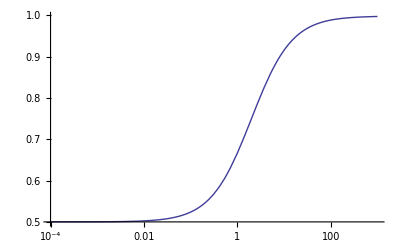

```mathematica
t=0.001
g=2
LogLinearPlot[-((1+(1+g t) x) (2 ⅇ^((4+t+g t) x) (1+g t) x-2 ⅇ^((1+g t+3 (1+t)) x) (1+g t) x+ⅇ^(4 (1+t) x) (1-(1+t) x)+ⅇ^(2 (2+g t) x) (1+(1+t) x)+ⅇ^(2 (2+t+g t) x) (-1+3 (1+t) x)-ⅇ^(2 (2+t) x) (1+3 (1+t) x)))/(2 ⅇ^((4+t+g t) x) x (-1+t-(1+t) x+(1+t)^2 x-(1+g t) x)+ⅇ^(4 (1+t) x) (-1+(1+t) x) (1+(1+g t) x)+ⅇ^(2 (2+t) x) (1+(3+t) x) (1+(1+g t) x)-ⅇ^(2 (2+g t) x) (1+(1+t) x) (1+(-2+3 (1+g t)) x)-ⅇ^(2 (2+t+g t) x) (-1+(5+t-3 (1+g t)) x+3 ((1+t) (-1+g t)+2 (1+g t)) x^2)+2 ⅇ^((1+g t+3 (1+t)) x) x (2+(1+t)^2 x+(1+g t) x-(1+t) (1+x))),{x,0.0001,1000}]
ClearAll[t,g]
```

```mathematica
(*Ok, now lets see if the first order correction due to curvature and stuff does something different*)
```

```mathematica
Simplify[Series[-((1+(1+t+g t) x) (2 ⅇ^((4+(2+g) t) x) (1+t+g t) x-2 ⅇ^((4+(4+g) t) x) (1+t+g t) x-ⅇ^(4 (1+t) x) (-1+x+t x)+ⅇ^(2 (2+t+g t) x) (1+x+t x)+ⅇ^(2 (2+(2+g) t) x) (-1+3 (1+t) x)-ⅇ^(2 (2+t) x) (1+3 (1+t) x)))/(2 ⅇ^((4+(2+g) t) x) x (-1+t-x-g t x+t^2 x)+ⅇ^(4 (1+t) x) (-1+x+t x) (1+(1+t+g t) x)+ⅇ^(2 (2+t) x) (1+(3+t) x) (1+(1+t+g t) x)-ⅇ^(2 (2+t+g t) x) (1+x+t x) (1+(1+3 (1+g) t) x)-ⅇ^(2 (2+(2+g) t) x) (-1+(2+t-3 (1+g) t) x+3 (1+(2+3 g) t+(1+g) t^2) x^2)+2 ⅇ^((4+(4+g) t) x) x (1+x+t^2 x+t (-1+(2+g) x))),{t,0,3}]]
```

(1+x)/(2+x)-((1+g) x^2 t)/(2+x)^2+(x^2 (12 x-3 g (2-5 x+x^2)-2 g^2 (2-3 x+x^2)) t^2)/(6 (2+x)^3)+1/(6 (2+x)^4)x^2 (2 g^3 x (4-4 x+3 x^2)+2 (4+12 x+x^2+6 x^3+x^4)+3 g (4+16 x-3 x^2+9 x^3+x^4)+g^2 (4+32 x-19 x^2+21 x^3+x^4)) t^3+O[t]^4

```mathematica
(*Oh, yes it does! It has the basic properties of a positive slope in both limits and does therefore show resonant behaviour.*)
```

0.1

1

1.1

1.2

0.8

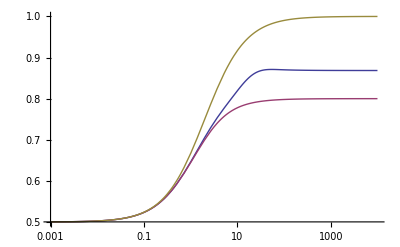

ClearAll::ssym: f' is not a symbol or a string.

```mathematica
t = 0.1
g = 1
a = 1+t
b = 1+(1+g)*t
xm = 4*t(g+1)
LogLinearPlot[{fklimuplus[a,b,x],(1+x)/(2+x)-((1+g) x^2 t)/(2+x)^2,(1+x)/(2+x)}, {x,0.001,10000}]
ClearAll[g,t,b,a,x,f,f']
```

```mathematica
f[x]:=(1+x)/(2+x)-((1+g) x^2 t)/(2+x)^2
```

```mathematica
D[f[x],x]
```

(2 (1+g) t x^2)/(2+x)^3-(2 (1+g) t x)/(2+x)^2-(1+x)/(2+x)^2+1/(2+x)

```mathematica
Expand[Simplify[(2+x)^3*((2 (1+g) t x^2)/(2+x)^3-(2 (1+g) t x)/(2+x)^2-(1+x)/(2+x)^2+1/(2+x))]]
```

```mathematica
ClearAll[g,t]
Solve[2+x-4 t x-4 g t x==0,x]
```

{{x→2/(-1+4 t+4 g t)}}

0.2

1

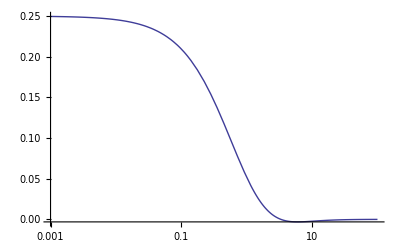

```mathematica
t = 0.2
g = 1
LogLinearPlot[(2 (1+g) t x^2)/(2+x)^3-(2 (1+g) t x)/(2+x)^2-(1+x)/(2+x)^2+1/(2+x),{x,0.001,100}]
```

```mathematica
Solve[Assuming[{x>0, g>1,t>0},{
(2 g t x^2)/(2+x)^3-(2 g t x)/(2+x)^2-(1+x)/(2+x)^2+1/(2+x)==0],x]
```

$Assumptions::fas: Warning: one or more assumptions evaluated to False.

{{x→2/(-1+4 t)}}

```mathematica
Simplify[D[f[x],x]/.g->(2+x)/(4 t x)]
```

0

```mathematica
(-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x-a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x-a ⅇ^(2 (1+b) x) x+3 b ⅇ^(2 (1+b) x) x+a ⅇ^(2 (a+b) x) x-3 b ⅇ^(2 (a+b) x) x-2 b ⅇ^((2+a+b) x) x+2 b ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2-a b ⅇ^(2 (1+a) x) x^2+3 a b ⅇ^(2 (1+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 b^2 ⅇ^((2+a+b) x) x^2+2 b^2 ⅇ^((3 a+b) x) x^2)/(-ⅇ^(4 a x)+ⅇ^(2 (1+a) x)-ⅇ^(2 (1+b) x)+ⅇ^(2 (a+b) x)+a ⅇ^(4 a x) x-b ⅇ^(4 a x) x+2 ⅇ^(2 (1+a) x) x-3 a ⅇ^(2 (1+a) x) x+b ⅇ^(2 (1+a) x) x+2 ⅇ^(2 (1+b) x) x-a ⅇ^(2 (1+b) x) x+b ⅇ^(2 (1+b) x) x-4 ⅇ^(2 (a+b) x) x+3 a ⅇ^(2 (a+b) x) x-b ⅇ^(2 (a+b) x) x-4 ⅇ^((2+a+b) x) x+2 a ⅇ^((2+a+b) x) x+4 ⅇ^((3 a+b) x) x-2 a ⅇ^((3 a+b) x) x+a b ⅇ^(4 a x) x^2+2 b ⅇ^(2 (1+a) x) x^2-3 a b ⅇ^(2 (1+a) x) x^2+2 a ⅇ^(2 (1+b) x) x^2+a b ⅇ^(2 (1+b) x) x^2-2 a ⅇ^(2 (a+b) x) x^2+2 b ⅇ^(2 (a+b) x) x^2-3 a b ⅇ^(2 (a+b) x) x^2-2 a ⅇ^((2+a+b) x) x^2+2 a^2 ⅇ^((2+a+b) x) x^2-2 b ⅇ^((2+a+b) x) x^2-2 a ⅇ^((3 a+b) x) x^2+2 a^2 ⅇ^((3 a+b) x) x^2+2 b ⅇ^((3 a+b) x) x^2)/.a->1+t
```

```mathematica
Simplify[(-ⅇ^(2 (1+b) x)-ⅇ^(4 (1+t) x)+ⅇ^(2 (2+t) x)+ⅇ^(2 (1+b+t) x)+3 b ⅇ^(2 (1+b) x) x-b ⅇ^(4 (1+t) x) x+b ⅇ^(2 (2+t) x) x-3 b ⅇ^(2 (1+b+t) x) x-2 b ⅇ^((3+b+t) x) x+2 b ⅇ^((b+3 (1+t)) x) x-ⅇ^(2 (1+b) x) (1+t) x+ⅇ^(4 (1+t) x) (1+t) x-ⅇ^(2 (2+t) x) (1+t) x+ⅇ^(2 (1+b+t) x) (1+t) x-2 b^2 ⅇ^((3+b+t) x) x^2+2 b^2 ⅇ^((b+3 (1+t)) x) x^2+3 b ⅇ^(2 (1+b) x) (1+t) x^2+b ⅇ^(4 (1+t) x) (1+t) x^2-b ⅇ^(2 (2+t) x) (1+t) x^2-3 b ⅇ^(2 (1+b+t) x) (1+t) x^2)/(-ⅇ^(2 (1+b) x)-ⅇ^(4 (1+t) x)+ⅇ^(2 (2+t) x)+ⅇ^(2 (1+b+t) x)+2 ⅇ^(2 (1+b) x) x+b ⅇ^(2 (1+b) x) x-b ⅇ^(4 (1+t) x) x+2 ⅇ^(2 (2+t) x) x+b ⅇ^(2 (2+t) x) x-4 ⅇ^(2 (1+b+t) x) x-b ⅇ^(2 (1+b+t) x) x-4 ⅇ^((3+b+t) x) x+4 ⅇ^((b+3 (1+t)) x) x-ⅇ^(2 (1+b) x) (1+t) x+ⅇ^(4 (1+t) x) (1+t) x-3 ⅇ^(2 (2+t) x) (1+t) x+3 ⅇ^(2 (1+b+t) x) (1+t) x+2 ⅇ^((3+b+t) x) (1+t) x-2 ⅇ^((b+3 (1+t)) x) (1+t) x+2 b ⅇ^(2 (2+t) x) x^2+2 b ⅇ^(2 (1+b+t) x) x^2-2 b ⅇ^((3+b+t) x) x^2+2 b ⅇ^((b+3 (1+t)) x) x^2+2 ⅇ^(2 (1+b) x) (1+t) x^2+b ⅇ^(2 (1+b) x) (1+t) x^2+b ⅇ^(4 (1+t) x) (1+t) x^2-3 b ⅇ^(2 (2+t) x) (1+t) x^2-2 ⅇ^(2 (1+b+t) x) (1+t) x^2-3 b ⅇ^(2 (1+b+t) x) (1+t) x^2-2 ⅇ^((3+b+t) x) (1+t) x^2-2 ⅇ^((b+3 (1+t)) x) (1+t) x^2+2 ⅇ^((3+b+t) x) (1+t)^2 x^2+2 ⅇ^((b+3 (1+t)) x) (1+t)^2 x^2)/.b->1+(1+g)*t]
```

(-2 ⅇ^((4+(2+g) t) x) (1+t+g t) x (1+(1+t+g t) x)+2 ⅇ^((4+(4+g) t) x) (1+t+g t) x (1+(1+t+g t) x)+ⅇ^(4 (1+t) x) (-1+x+t x) (1+(1+t+g t) x)-ⅇ^(2 (2+t) x) (-1+x+t x) (1+(1+t+g t) x)+ⅇ^(2 (2+t+g t) x) (1+x+t x) (-1+3 (1+t+g t) x)-ⅇ^(2 (2+(2+g) t) x) (1+x+t x) (-1+3 (1+t+g t) x))/(2 ⅇ^((4+(2+g) t) x) x (-1+t-x-g t x+t^2 x)+ⅇ^(4 (1+t) x) (-1+x+t x) (1+(1+t+g t) x)-ⅇ^(2 (2+t) x) (-1+x+3 t x) (1+(1+t+g t) x)+ⅇ^(2 (2+t+g t) x) (1+x+t x) (-1+(3+t+g t) x)-ⅇ^(2 (2+(2+g) t) x) (-1+(2+(-2+g) t) x+(3+(6+g) t+3 (1+g) t^2) x^2)+2 ⅇ^((4+(4+g) t) x) x (1+x+t^2 x+t (-1+(2+g) x)))

```mathematica
Simplify[Series[(-2 ⅇ^((4+(2+g) t) x) (1+t+g t) x (1+(1+t+g t) x)+2 ⅇ^((4+(4+g) t) x) (1+t+g t) x (1+(1+t+g t) x)+ⅇ^(4 (1+t) x) (-1+x+t x) (1+(1+t+g t) x)-ⅇ^(2 (2+t) x) (-1+x+t x) (1+(1+t+g t) x)+ⅇ^(2 (2+t+g t) x) (1+x+t x) (-1+3 (1+t+g t) x)-ⅇ^(2 (2+(2+g) t) x) (1+x+t x) (-1+3 (1+t+g t) x))/(2 ⅇ^((4+(2+g) t) x) x (-1+t-x-g t x+t^2 x)+ⅇ^(4 (1+t) x) (-1+x+t x) (1+(1+t+g t) x)-ⅇ^(2 (2+t) x) (-1+x+3 t x) (1+(1+t+g t) x)+ⅇ^(2 (2+t+g t) x) (1+x+t x) (-1+(3+t+g t) x)-ⅇ^(2 (2+(2+g) t) x) (-1+(2+(-2+g) t) x+(3+(6+g) t+3 (1+g) t^2) x^2)+2 ⅇ^((4+(4+g) t) x) x (1+x+t^2 x+t (-1+(2+g) x))),{t,0,4}]]
```

1+(g t)/4+1/48 g (12 (-1+x)+g (-8+9 x)) t^2-1/192 (g (16 (-3+3 x+x^2)+4 g (-16+14 x+3 x^2)+g^2 (-16+16 x+5 x^2))) t^3+1/11520 g (960 (-3+3 x+x^2)+g^3 (-320+160 x+368 x^2-105 x^3)-60 g^2 (48-32 x-19 x^2+x^3)+80 g (-72+57 x+19 x^2+3 x^3)) t^4+O[t]^5

0.01

1

1.01

1.02

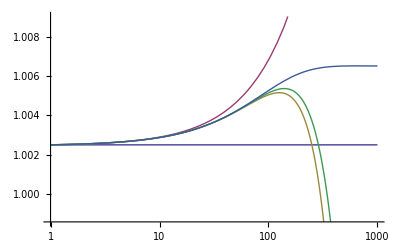

```mathematica
t = 0.01
g = 1
a = 1+t
b = 1+(1+g)*t
LogLinearPlot[{1+(g t)/4,1+(g t)/4+1/48 g (12 (-1+x)+g (-8+9 x)) t^2,1+(g t)/4+1/48 g (12 (-1+x)+g (-8+9 x)) t^2-1/192 (g (16 (-3+3 x+x^2)+4 g (-16+14 x+3 x^2)+g^2 (-16+16 x+5 x^2))) t^3,1+(g t)/4+1/48 g (12 (-1+x)+g (-8+9 x)) t^2-1/192 (g (16 (-3+3 x+x^2)+4 g (-16+14 x+3 x^2)+g^2 (-16+16 x+5 x^2))) t^3+1/11520 g (960 (-3+3 x+x^2)+g^3 (-320+160 x+368 x^2-105 x^3)-60 g^2 (48-32 x-19 x^2+x^3)+80 g (-72+57 x+19 x^2+3 x^3)) t^4,fklimuminus[a,b,x]}, {x,1,1000}]
```